## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = False;
removeOutputFiles = False;

rxnName="PGMd";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = False; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)


(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit_PGMd";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGMd/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName,  assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological];
```

{3pg,Null,Keq substrate}

{0.189,Keq value}

{3pg,Km or S05 substrate}

{0.0002,Km or S05 value}

{2pg,Km or S05 substrate}

{0.00019,Km or S05 value}

{{{3pg,Null},{23dpg,0.0001}},kcat substrates}

{330,kcat value}

{{{2pg,Null},{23dpg,0.0001}},kcat substrates}

{220,kcat value}

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 0.189 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 330 | 319.
341. | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 220 | 207.
233. | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
KeqList0[[1]][[3]]=0.7;
```

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

((3pg)^c⇌(2pg)^c)^PGMd

;

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg,Null | 0.7 | 0.17955
0.19845 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | 0.0002 | 0.000173
0.000227 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | 0.00019 | 0.000155
0.000225 | 23dpg | 0.0001 | M | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | 3pg | Null
23dpg | 0.0001 | 330 | 319.
341. | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02
1 | 2pg | Null
23dpg | 0.0001 | 220 | 207.
233. | 1/s | 7 | 30 | trishcl | 0.03 | mg2 | 0.005
so4 | 0.005
cl | 0.02
k | 0.02

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
catalyticBranch={"E_PGMd[c] + 23dpg[c] <=> E_PGMd[c]&23dpg",
				"E_PGMd[c]&23dpg + 3pg[c] <=> E_PGMd[c]&23dpg&3pg",
				"E_PGMd[c]&23dpg&3pg <=> E_PGMd[c]&23dpg&2pg",
				"E_PGMd[c]&23dpg&2pg <=> E_PGMd[c]&23dpg + 2pg[c]"};

enzymeModelOrig=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModelOrig["Reactions"]
```

{((PGMd^c)_^+(23dpg)^c⇌(PGMd^c&(23dpg)^c)_^)^PGMd1,((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,((PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c)^PGMd3,((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PGMd^c&(23dpg)^c)_^+(3pg)^c⇌(PGMd^c&(23dpg)^c&(3pg)^c)_^)^PGMd2,Overscript[(PGMd^c&(23dpg)^c&(2pg)^c)_^⇌(PGMd^c&(23dpg)^c)_^+(2pg)^c, PGMd3],((PGMd^c&(23dpg)^c&(3pg)^c)_^⇌(PGMd^c&(23dpg)^c&(2pg)^c)_^)^PGMd4};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModelOrig, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites];
```

{(3pg)^c→0}

{(2pg)^c→0}

{(3pg)^c→∞}

{(2pg)^c→∞}

Added inhibition reactions:

{}

Loading flux equation...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
PGMdRateConsts=finalRateConsts
Export[inputPath<>"/"<>rxnName<>"_rateConsts.m",PGMdRateConsts, "MX"]
```

{k_PGMd1^⟵,k_PGMd1^⟶,k_PGMd2^⟵,k_PGMd2^⟶,k_PGMd3^⟵,k_PGMd3^⟶,k_PGMd4^⟵,k_PGMd4^⟶}

/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGMd/fit_PGMd/input/PGMd_rateConsts.m

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint@dataPathList
```

Priority	23dpg[c]	2pg[c]	3pg[c]	param_PGMd_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0	0	0	1	7.5	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/haldaneRatio_1.txt"	0.7
1	0.0001	0	0.00002	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.09090909090909091
1	0.0001	0	0.00003169786384922229	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.13680688860321008
1	0.0001	0	0.00005023772863019165	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.2007600089131019
1	0.0001	0	0.00007962143411069939	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.2847472489508013
1	0.0001	0	0.0001261914688960386	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.38686317984685686
1	0.0001	0	0.00020000000000000004	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.5
1	0.0001	0	0.0003169786384922229	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.6131368201531432
1	0.0001	0	0.0005023772863019165	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.7152527510491988
1	0.0001	0	0.0007962143411069948	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.7992399910868982
1	0.0001	0	0.0012619146889603862	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.8631931113967899
1	0.0001	0	0.0020000000000000005	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateFor_3pg.txt"	0.9090909090909091
1	0.0001	0.000018999999999999994	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.09090909090909087
1	0.0001	0.00003011297065676116	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.13680688860321003
1	0.0001	0.00004772584219868205	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.20076000891310186
1	0.0001	0.0000756403624051644	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.2847472489508012
1	0.0001	0.00011988189545123664	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.38686317984685686
1	0.0001	0.00018999999999999996	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.49999999999999994
1	0.0001	0.0003011297065676116	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.6131368201531432
1	0.0001	0.0004772584219868205	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.7152527510491987
1	0.0001	0.0007564036240516448	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.7992399910868982
1	0.0001	0.0011988189545123664	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.8631931113967899
1	0.0001	0.0018999999999999996	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/relRateRev_2pg.txt"	0.9090909090909092
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0	0.01	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateFor.txt"	330
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220
1	0.0001	0.01	0	1	7	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/glycolysis/PGM_d/fit_PGMd/input/absRateRev.txt"	220

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=50;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 0.972311013676
best_fit: 0.796344964292
best_fit: 0.491518285883
best_fit: 0.837410199535
best_fit: 1.05471485397
best_fit: 1.0594055411
best_fit: 1.04695903411
best_fit: 1.06149440228
best_fit: 1.02188014101
best_fit: 0.804816085962
best_fit: 0.999495837421
best_fit: 0.853723606266
best_fit: 0.87850038669
best_fit: 0.954900593519
best_fit: 0.505159535289
best_fit: 1.01644348933
best_fit: 1.06998571294
best_fit: 0.659444444547
best_fit: 1.06418174167
best_fit: 1.01310108879
best_fit: 0.986914508215
best_fit: 0.76383201549
best_fit: 0.993545015732
best_fit: 1.01970831291
best_fit: 0.969125196925
best_fit: 1.09989970937
best_fit: 1.0938293451
best_fit: 0.596015385296
best_fit: 0.492640984688
best_fit: 1.0058074036
best_fit: 0.977605370963
best_fit: 0.90497036078
best_fit: 0.492906237704
best_fit: 1.07923351112
best_fit: 0.74059291678
best_fit: 0.826939583376
best_fit: 1.0302199165
best_fit: 0.647417544626
best_fit: 1.04952942139
best_fit: 0.723236371433
best_fit: 0.930369122083
best_fit: 0.671260157553
best_fit: 0.677095701382
best_fit: 1.03186471096
best_fit: 1.02254766187
best_fit: 0.614015043993
best_fit: 0.620082700861
best_fit: 0.567965221914
best_fit: 1.0825214719
best_fit: 0.813333995754

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | haldaneRatio_1 | 0.00973195 | 0.0000947108 | 0.0158631 | 2.26616 | 0.7 | 0.715863
1 | relRateFor_3pg | 0.139755 | 0.0195314 | 0.0250141 | 27.5155 | 0.0909091 | 0.065895
1 | relRateFor_3pg | 0.133679 | 0.0178701 | 0.0362461 | 26.4943 | 0.136807 | 0.100561
1 | relRateFor_3pg | 0.125069 | 0.0156424 | 0.0502353 | 25.0226 | 0.20076 | 0.150525
1 | relRateFor_3pg | 0.113497 | 0.0128816 | 0.0654857 | 22.9978 | 0.284747 | 0.219262
1 | relRateFor_3pg | 0.0989982 | 0.00980063 | 0.0788571 | 20.3837 | 0.386863 | 0.308006
1 | relRateFor_3pg | 0.0823482 | 0.00678123 | 0.0863607 | 17.2721 | 0.5 | 0.413639
1 | relRateFor_3pg | 0.0650344 | 0.00422947 | 0.0852717 | 13.9074 | 0.613137 | 0.527865
1 | relRateFor_3pg | 0.0487915 | 0.00238061 | 0.0760067 | 10.6266 | 0.715253 | 0.639246
1 | relRateFor_3pg | 0.0349613 | 0.00122229 | 0.0618184 | 7.73464 | 0.79924 | 0.737422
1 | relRateFor_3pg | 0.0241267 | 0.000582096 | 0.0466459 | 5.40388 | 0.863193 | 0.816547
1 | relRateFor_3pg | 0.0161808 | 0.000261819 | 0.0332474 | 3.65722 | 0.909091 | 0.875843
1 | relRateRev_2pg | 0.137366 | 0.0188693 | 0.0338215 | 37.2036 | 0.0909091 | 0.124731
1 | relRateRev_2pg | 0.129284 | 0.0167143 | 0.0474364 | 34.674 | 0.136807 | 0.184243
1 | relRateRev_2pg | 0.118268 | 0.0139873 | 0.0628397 | 31.3009 | 0.20076 | 0.2636
1 | relRateRev_2pg | 0.104213 | 0.0108603 | 0.0772225 | 27.1197 | 0.284747 | 0.36197
1 | relRateRev_2pg | 0.0877149 | 0.00769391 | 0.0865848 | 22.3813 | 0.386863 | 0.473448
1 | relRateRev_2pg | 0.0701398 | 0.00491959 | 0.0876379 | 17.5276 | 0.5 | 0.587638
1 | relRateRev_2pg | 0.0532483 | 0.00283539 | 0.0799789 | 13.0442 | 0.613137 | 0.693116
1 | relRateRev_2pg | 0.0385467 | 0.00148585 | 0.0663862 | 9.2815 | 0.715253 | 0.781639
1 | relRateRev_2pg | 0.0268172 | 0.000719162 | 0.0509077 | 6.36952 | 0.79924 | 0.850148
1 | relRateRev_2pg | 0.0180934 | 0.00032737 | 0.0367216 | 4.25416 | 0.863193 | 0.899915
1 | relRateRev_2pg | 0.0119388 | 0.000142534 | 0.0253376 | 2.78714 | 0.909091 | 0.934429
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateFor | 4.28659×10^-8 | 1.83749×10^-15 | 0.0000325718 | 9.87025×10^-6 | 330 | 330.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.
1 | absRateRev | 1.02361×10^-7 | 1.04779×10^-14 | 0.0000518531 | 0.0000235696 | 220 | 220.

### Simulated Data and Best Fit Data Plot

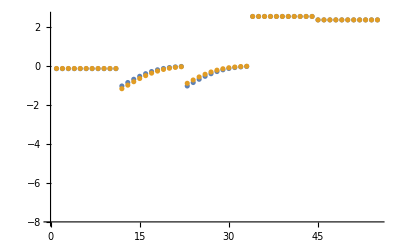

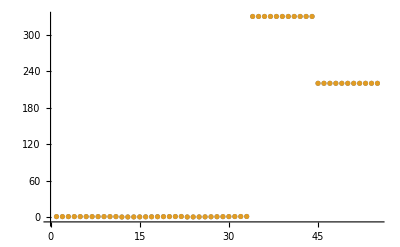

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 1;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.000045 | 0.000045 | 2.51272×10^-6
0.00089 | 0.00089 | 1.39821×10^-6
0.00053 | 0.00053 | 1.35758×10^-6

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
268 | 268. | 3.33383×10^-6

```mathematica
backCalculateRatios[customRatiosDataList[[1]][[2]], customRatiosDataList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
425. | 425. | 8.29398×10^-6

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.452 | 0.452 | 4.57492×10^-6